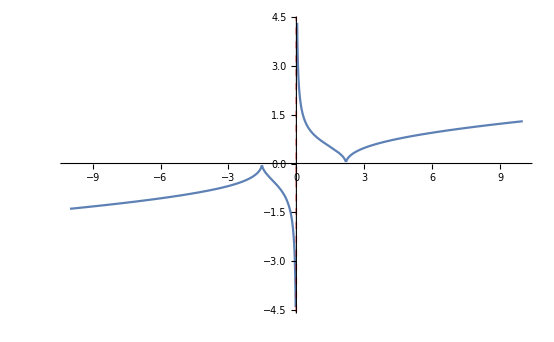

D(x) = (-∞,+∞)

E(y) = (0, +∞)

Функция не четна

Функция не нечетна

Функция не периодическая

Пересечения с осью абсцисс:

{{x→1/3 (1-√31)},{x→1/3 (1+√31)}}

Пересечения с осью ординат:

{}

Как видно по графику функция возрастает на промежутках (-∞, 1/3 (1-√31)] и [1/3 (1+√31), +∞) и убывает на промежутках [1/3 (1-√31), 0),(0, 1/3 (1+√31)]"

Аналогично, функция отрицательна на промежутках (-∞, 1/3 (1-√31)) и (1/3 (1-√31), 0) и положительна на промежутках (0, 1/3 (1+√31)) и (1/3 (1+√31), +∞)"

Точки экстремума - x = 1/3 (1-√31) и x = 1/3 (1+√31), значение функции в них равно 0"

Единственная точка разрыва - x = 0. Так как lim(f(x)) для x -> 0- равен -∞, а lim(f(x)) для x -> 0+ равен ∞, то это разрыв типа полюс, что подтверждается графиком.

Вертикальные ассимптоты: x = 0. Горизонтальные ассимптоты: отсутствуют, так как lim(f(x)) при x -> ∞ равен ∞. Наклонные ассимптоты: отсутствуют, так как при k = lim(f(x) / x) при x -> ∞, равном 0, b = lim(f(x) - kx) при x -> ∞ равен ∞.

```mathematica
task := Sqrt[Abs[3*x^3 - 2*x^2 - 10*x]] / (4*x)
f [y_] := task /.x -> y;
d := D[f[x], x]
p := Plot [f [x], {x, -10, 10}]
asym := Graphics [{Thick, Red, Dashed, Line[{{0, -5} , {0, 5}}]}]
Show [{p, asym}]
Print ["D(x) = (-∞,+∞)"]
Print ["E(y) = (0, +∞)"]
chet := f[x]==f[-x]//TautologyQ
nechet := f[-x] == -f[x]//TautologyQ
period := FunctionPeriod[f[x],x] == 0//TautologyQ
If  [chet,Print["Функция четна"],Print["Функция не четна"]]
If  [nechet,Print["Функция нечетна"],Print["Функция не нечетна"]]
If  [period,Print["Функция не периодическая"],Print["Функция периодическая"]]
Print["Пересечения с осью абсцисс:"]
Solve[f[x] == 0 ,x ]
Print["Пересечения с осью ординат:"]
Solve [f [x] == y &&  x == 0, y]
Print[""]
Print["Как видно по графику функция возрастает на промежутках (-∞, \!\(\*FractionBox[\(1\), \(3\)]\) (1-\!\(\*SqrtBox[\(31\)]\))] и [\!\(\*FractionBox[\(1\), \(3\)]\) (1+\!\(\*SqrtBox[\(31\)]\)), +∞) и убывает на промежутках [\!\(\*FractionBox[\(1\), \(3\)]\) (1-\!\(\*SqrtBox[\(31\)]\)), 0),(0, \!\(\*FractionBox[\(1\), \(3\)]\) (1+\!\(\*SqrtBox[\(31\)]\))]\""]
Print ["Аналогично, функция отрицательна на промежутках (-∞, \!\(\*FractionBox[\(1\), \(3\)]\) (1-\!\(\*SqrtBox[\(31\)]\))) и (\!\(\*FractionBox[\(1\), \(3\)]\) (1-\!\(\*SqrtBox[\(31\)]\)), 0) и положительна на промежутках (0, \!\(\*FractionBox[\(1\), \(3\)]\) (1+\!\(\*SqrtBox[\(31\)]\))) и (\!\(\*FractionBox[\(1\), \(3\)]\) (1+\!\(\*SqrtBox[\(31\)]\)), +∞)\""]

Print ["Точки экстремума - x = \!\(\*FractionBox[\(1\), \(3\)]\) (1-\!\(\*SqrtBox[\(31\)]\)) и x = \!\(\*FractionBox[\(1\), \(3\)]\) (1+\!\(\*SqrtBox[\(31\)]\)), значение функции в них равно 0\""]
Print["Единственная точка разрыва - x = 0. Так как lim(f(x)) для x -> 0- равен ", Limit[f[x],x->0,Direction ->"FromBelow"], ", а lim(f(x)) для x -> 0+ равен ", Limit[f[x],x->0,Direction ->"FromAbove"], ", то это разрыв типа полюс, что подтверждается графиком."]
Print["Вертикальные ассимптоты: x = 0. Горизонтальные ассимптоты: отсутствуют, так как lim(f(x)) при x -> ∞ равен ", Limit[f[x],x->∞], ". Наклонные ассимптоты: отсутствуют, так как при k = lim(f(x) / x) при x -> ∞, равном ", Limit[f[x] / x ,x->∞], ", b = lim(f(x) - kx) при x -> ∞ равен ",  Limit[f[x] - Limit[f[x] / x ,x->∞] * x ,x->∞],"."]
```